## Stuff

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.01;
h=0.01;
c=0.05;
n=100;
timeSteps=10/Δt;
fps=1/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==j,1,If[i==j+1 ||i==j-1,1/4,0]]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}];
LHS//MatrixForm;

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[i==j(*||i==1||i==n*),0,If[i==j+1,-3/(4h),If[i==j-1,3/(4h),0]]]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}];
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix*)
inverseLHS=Inverse[LHS];

(*Create discrete list of the function progressing through time*)
ϕT={ϕ};

For[i=0,i<timeSteps,i++,
(*Calculate the function at the next time step using the CFD*)
last=ϕT[[Length[ϕT]]];
new=last-c Δt inverseLHS.RHS.last;
ϕT=Append[ϕT,new];

(*Force the boundary conditions*)
(*ϕT[[Length[ϕT]]][[1]]=0;*)
]

(*Generate a select list of Plots from the total discrete list of functions through time*)
plots={};
numPlots=50;
For[i=0,i<=numPlots,i++,
plots=Append[plots,ListPlot[ϕT[[Floor[Max[i*Length[ϕT]/numPlots,1]]]],PlotRange->{-2,2},Joined->False]];
]

(*Animate the Plots*)
ListAnimate[plots,fps*numPlots/timeSteps]
```

## More Stuff

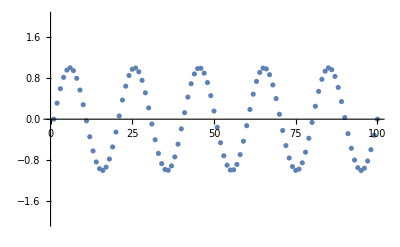

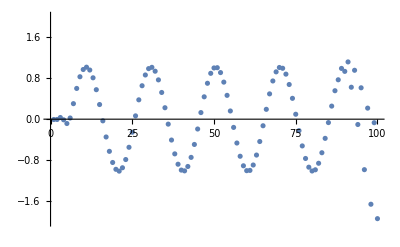

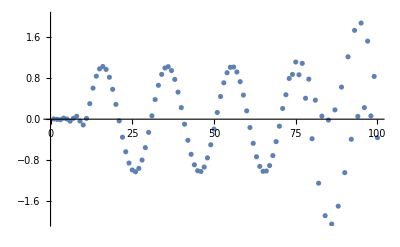

```mathematica
Clear["`*"];

(*Define Variables*)
Δt=0.01;
h=0.01;
c=0.05;
n=100;
timeSteps=2/Δt;

(*Create function initial condition as discrete list*)
ϕ=Array[Sin[10π#]&,n,{0,1}];

(*Generate the LHS Matrix for the CFD*)
LHSRow[i_,j_]:=Module[{},
If[i==j,1,If[i==j+1 ||i==j-1,1/4,0]]
]
LHS=Array[LHSRow[#1,#2]&,{n,n}];
LHS//MatrixForm;

(*Generate the RHS Matrix for the CFD*)
RHSRow[i_,j_]:=Module[{},
If[i==j(*||i==1||i==n*),0,If[i==j+1,-3/(4h),If[i==j-1,3/(4h),0]]]
]
RHS=Array[RHSRow[#1,#2]&,{n,n}];
RHS//MatrixForm;

(*Find the Inverse of the LHS Matrix and the Q matrix*)
inverseLHS=Inverse[LHS];
Q=inverseLHS.RHS;

updateFunction[steps_]:=Module[{},
For[i=0,i<steps,i++,ϕ=ϕ-c Δt Q.ϕ]
]
plotFunction[]:=Module[{},
ListPlot[ϕ,PlotRange->{-2,2},Joined->False]
]

plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]

updateFunction[timeSteps/2]
plotFunction[]
```